# Boundary Crossing of Order Statistics Point Processes

## Supplementary material I: Simulation study and statistical applications

Online accompaniement for the original research paper “Boundary Crossing of Order Statistics Point Processes”

## Simulation study and statistical applications

The goal of this section is to show the statistical potential of the formulas associated to the survival function of the crossing time τ_β given by

#### ℙ(τ_β>t)=𝔼{A_(N(t))[1│ F_t(β_1),...,F_t(β_(N(t)))]𝕀_{N(t)≤ h(t)+β}} (1)

The survival function of the crossing time could be evaluated by using a Crude Monte Carlo procedure,

#### ℙ(τ_β>t)=𝔼{𝕀_{τ_β>t}} (2)

However, we might face problem linked to rare event simulations. The variance of the CMC estimator will be of the same magnitude as the quantity of interest. Variance reduction techniques are typically used in those situations. The goal of this numerical study is to show that the Monte Carlo estimator based on formula (1) permits a reduction of the variance. We also discuss the relevance of formula (1) for statistical application.

It is easily seen that

#### σ_CMC⩾σ_APMC,

see the paper for more details. The amplitude of the reduction is difficult to assess as it depends on the parameters of both the OSPP and the boundary.

consider a Polya-Lundberg process of parameter λ>0, and b≥0. It corresponds to a linear birth process of rate λ_n(t)=λ(1+bn)/(1+λt). The intensity of the mixed Poisson process is gamma distributed a priori Γ(1/b,λb), where 1/b is the shape parameter and m is the mean parameter.

```mathematica
SetDirectory[NotebookDirectory[]];
Import["/Users/pierrogoffard/Dropbox/PO/Article/AppellPolynomialClaudePO/FirstCrossingFirstMeeting/Mathematica/BoundaryCrossingOSPPBoundaryPackage.wl"]
λ=2;b=1;W = GammaDistribution[1/b,λ*b];
```

The time is assumed to flow as usual, and

```mathematica
ν=Function[{t},t];
Inverseν=Function[{t},t];
```

The shape of the upper boundary is polynomial

```mathematica
h=Function[{t},c*t^(d)];
Inverseh=Function[{t},(t/c)^(1/d)];
```

with parameters

```mathematica
c=1;d=2;
```

and starts at (0,β), where

```mathematica
β=3/2;
```

The time horizon is set to

```mathematica
t=2;
```

The following figure displays 5 trajectories from the studied OSPP up to time t, along with the upper boundary,

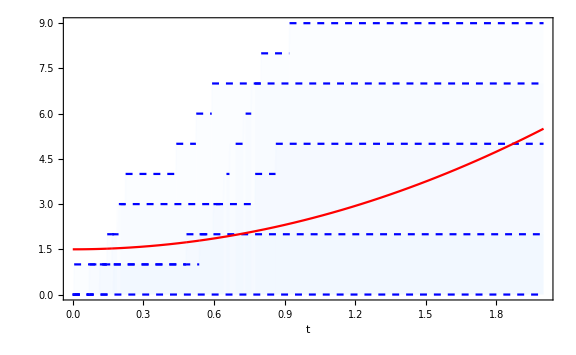

```mathematica
(*Trajectories=SampleMPTTTrajectory[W,ν,Inverseν,t,5];
PlotTrajectoriesMPTTUpperBoundary[Trajectories,h,β,16,Large]
Export["OSPPTrajectoriesUpperBound.png",%];*)
```

The trajectories falls into three categories

The ones ending below β,

The ones ending above h(t)+β,

The ones ending in between β and h(t)+β.

In the first case, both A_(N(t))[1│ F_t(β_1),...,F_t(β_(N(t)))]𝕀_{N(t)≤ h(t)+β} and 𝕀_{τ_β>t} evaluates to 1, as no crossing is possible. In the second case, both A_(N(t))[1│ F_t(β_1),...,F_t(β_(N(t)))]𝕀_{N(t)≤ h(t)+β} and  𝕀_{τ_β>t} evaluates to 0 as crossing is almost sure. In the third case 𝕀_{τ_β>t} evaluates either to 1 or 0 while A_(N(t))[1│ F_t(β_1),...,F_t(β_(N(t)))]𝕀_{N(t)≤ h(t)+β} evaluates to some p⩽1. The following Table stacks the value of A_(N(t))[1│ F_t(β_1),...,F_t(β_(N(t)))]𝕀_{N(t)≤ h(t)+β} and 𝕀_{τ_β>t} for the different trajectories,

```mathematica
TeXForm[N[CMCvsAppellMCMPTTUpperBoundary[Trajectories,ν,t,h,Inverseh,β]]]
MatrixForm[N[CMCvsAppellMCMPTTUpperBoundary[Trajectories,ν,t,h,Inverseh,β]]]
```

The variance is in fact reduced when a lot of trajectories are finishing their run between β and h(t)+β, as otherwise A_(N(t))[1│ F_t(β_1),...,F_t(β_(N(t)))]𝕀_{N(t)≤ h(t)+β}= 𝕀_{τ_β>t}. In our example the probability of interest is evaluated exactly by formula (1)

```mathematica
N[SurvivalCrossingTimeMPTTUpperBoundary[W,ν,t,h,Inverseh,β]]
```

0.568265

The variance associated to the APMC estimator is

```mathematica
N[VarianceAPMCCrossingTimeMPTTUpperBoundary[W,ν,t,h,Inverseh,β]]
```

0.184338

while the one of the CMC estimatotr is

```mathematica
N[VarianceCMCCrossingTimeMPTTUpperBoundary[W,ν,t,h,Inverseh,β]]
```

0.24534

The use of formula (1) permits indeed to remove the variability induced by the jump times and implies better result when they actually influence the crossing time, namely when the likelihood of N(t) being between β and h(t)+β is high. We can appreciate that fact by considering the evolution of the variance of the two Monte Carlo estimators with the time horizon t. The probabity of N(t) being between U and h(t)+U is indeed increasing

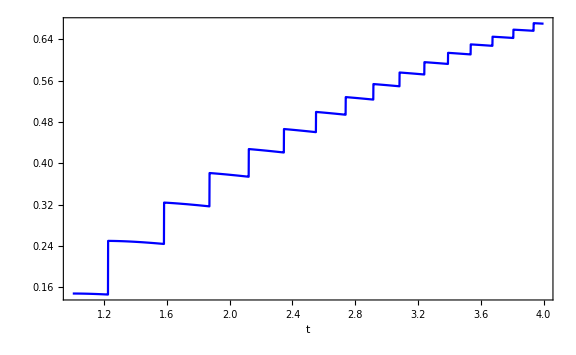

```mathematica
Plot[Sum[PDFMPTT[W,ν,n,t],{n,Floor[β]+1,Floor[h[t]+β],1}],{t,1,4},PlotRange->All,PlotStyle->Blue,ImageSize->Large,LabelStyle->Directive[Black,16],AxesLabel->{"t",""},Frame->True,FrameLabel->{{"",""},{"t",""}}]
Export["PDFNt.png",%];
```

On the left hand side, the variance of the CMC estimator and the APMC estimator are plotted for different time horizon. On the right-hand side the relative difference (σ_APMC^2-σ_CMC^2)/σ_CMC^2.

```mathematica
PlotVarianceCMCAPMCrossingTimeMPTTUpperBoundary[W,ν,4,h,Inverseh,β,16,Full]
Export["VarianceCMCVsAPMC.png",%];
```

-Graphics-

The following table gives some values of the variance of the two estimator, the probability of no crossing and the relative difference for several time horizons

```mathematica
N[SurvivalCrossingTimeMPTTUpperBoundary[W,ν,4,h,Inverseh,β]]
```

0.562619

```mathematica
TeXForm[N[Table[{t,
SurvivalCrossingTimeMPTTUpperBoundary[W,ν,t,h,Inverseh,β]
,VarianceAPMCCrossingTimeMPTTUpperBoundary[W,ν,t,h,Inverseh,β],VarianceCMCCrossingTimeMPTTUpperBoundary[W,ν,t,h,Inverseh,β],
DeltaVarianceCMCAPMCCrossingTimeMPTTUpperBoundary[W,ν,t,h,Inverseh,β]}
,{t,1,4,1}]]]
```

\left(
\begin{array}{ccccc}
 1. & 0.62963 & 0.196159 & 0.233196 & -15.8824 \\
 2. & 0.568265 & 0.184338 & 0.24534 & -24.8643 \\
 3. & 0.562963 & 0.167682 & 0.246036 & -31.8464 \\
 4. & 0.562619 & 0.158262 & 0.246079 & -35.6867 \\
\end{array}
\right)

The fact that the APMC estimator is better from a variance point of view implies that it will be a more reliable statistical estimator if data were to be available. The other appealing feature is that we only need the number of jumps up to time t to evaluate the APMC estimator, it is not necessary to keep track of the jump times which are in practical situation often unknown. The cost is of course the parametric assumption we make by stating that we are dealing with an OSPP, of which the associated μ(t) function has to be identified. We can argue that the mixed Poisson process alone is widely used for modelization purposes and is well suited for many phenomena. The reader is now encouraged to try out some parametrization of the OSPP or the upper boundary and see how large (or how little) the reduction of variance may be in different situation. Hereafter the different shape for the upper boundary

```mathematica
MatrixForm[ShapeFunctions={{"Polynomial",Function[{x},c*x^(d)],Function[{x},(x/c)^(1/d)]},{"Exponential",Function[{x},c*(Exp[d*x]-1)],Function[{x},Log[x/c+1]/d]},{"Logarithmic",Function[{x},c*Log[1+d*x]],Function[{x},(Exp[x/c]-1)/d]}}]
```

(Polynomial | Function[{x},c x^d] | Function[{x},(x/c)^(1/d)]
Exponential | Function[{x},c (Exp[d x]-1)] | Function[{x},Log[x/c+1]/d]
Logarithmic | Function[{x},c Log[1+d x]] | Function[{x},(Exp[x/c]-1)/d])

### Variance reduction for Mixed Poisson process with a time transformation

We consider the case of the homogeneous Poisson process hereafter. We can first have a look at the probability ℙ[U⩽N(t)⩽h(t)+U] as it closely linked to the reduction of the variance imlied y the use of the APMC estimator,

```mathematica
Manipulate[
W=TransformedDistribution[λ*B,B\[Distributed]BinomialDistribution[1,1]];ν=Function[{t},t];
cTemp=c;
dTemp=d;
ShapeFunctions={{"Polynomial",Function[{x},cTemp*x^(dTemp)],Function[{x},(x/cTemp)^(1/dTemp)]},{"Exponential",Function[{x},cTemp*(Exp[dTemp*x]-1)],Function[{x},Log[x/cTemp+1]/dTemp]},{"Logarithmic",Function[{x},cTemp*Log[1+dTemp*x]],Function[{x},(Exp[x/cTemp]-1)/dTemp]}};
h=shape;
Plot[Sum[PDFMPTT[W,ν,n,t],{n,Floor[β],Floor[h[t]+β],1}],{t,1,4},PlotRange->All,PlotStyle->Blue,ImageSize->Large,LabelStyle->Directive[Black,16],AxesLabel->{"t",""},Frame->True,FrameLabel->{{"",""},{"t","ℙ[β⩽N(t)⩽h(t)+β]"}}]
,{{λ,1,Style["Intensity of the Poisson process",Blue,14]},1,5,1/2}
,{{β,0,Style["β",Blue,14]},0,5,1/2}
,{{shape,ShapeFunctions[[1,2]],Style["Shape of boundary",Blue,14]},
Table[ShapeFunctions[[k,2]]->Style[ShapeFunctions[[k,1]],Black,14],{k,1,Length[ShapeFunctions]}]}
,{{c,1,Style["c",Blue,14]},1,5,0.5}
,{{d,0.5,Style["d",Blue,14]},0.5,2,0.5}
]
```

And then of course see what happens in term of variance

```mathematica
Manipulate[
W=TransformedDistribution[λ*B,B\[Distributed]BinomialDistribution[1,1]];ν=Function[{t},t];
cTemp=c;
dTemp=d;
ShapeFunctions={{"Polynomial",Function[{x},cTemp*x^(dTemp)],Function[{x},(x/cTemp)^(1/dTemp)]},{"Exponential",Function[{x},cTemp*(Exp[dTemp*x]-1)],Function[{x},Log[x/cTemp+1]/dTemp]},{"Logarithmic",Function[{x},cTemp*Log[1+dTemp*x]],Function[{x},(Exp[x/cTemp]-1)/dTemp]}};
h=ShapeFunctions[[k,2]];
Inverseh=ShapeFunctions[[k,3]];
PlotVarianceCMCAPMCrossingTimeMPTTUpperBoundary[W,ν,4,h,Inverseh,β,16,Full]
,{{λ,1,Style["Intensity of the Poisson process",Blue,14]},1,5,1/2}
,{{β,0,Style["β",Blue,14]},0,5,1/2}
,{{k,1,Style["Shape of boundary",Blue,14]},Table[i->Style[ShapeFunctions[[i,1]],Black,14],{i,1,3}]}
(*,{{k,1,Style["Shape of boundary",Blue,14]},
,{k,1,Length[ShapeFunctions]}]}*)
,{{c,1,Style["c",Blue,14]},1,5,0.5}
,{{d,0.5,Style["d",Blue,14]},0.5,2,0.5}
]
```

### Variance reduction for mixed sample process

The same study may be conducted for the mixed sample process. We consider hereafter a linear death process. Again the probability ℙ[U⩽N(t)⩽h(t)+U] gives insight on the variance reduction,

```mathematica
Manipulate[
Z=TransformedDistribution[z*B,B\[Distributed]BinomialDistribution[1,1]];
μ=Function[{t},z(1-Exp[-b*t])];
cTemp=c;
dTemp=d;
ShapeFunctions={{"Polynomial",Function[{x},cTemp*x^(dTemp)],Function[{x},(x/cTemp)^(1/dTemp)]},{"Exponential",Function[{x},cTemp*(Exp[dTemp*x]-1)],Function[{x},Log[x/cTemp+1]/dTemp]},{"Logarithmic",Function[{x},cTemp*Log[1+dTemp*x]],Function[{x},(Exp[x/cTemp]-1)/dTemp]}};
h=shape;
Plot[Sum[PDFMSP[Z,μ,z,n,t],{n,Floor[β],Floor[h[t]+β],1}],{t,1/10,4},PlotRange->All,PlotStyle->Blue,ImageSize->Large,LabelStyle->Directive[Black,16],AxesLabel->{"t",""},Frame->True,FrameLabel->{{"",""},{"t","ℙ[β⩽N(t)⩽h(t)+β]"}}]
,{{z,5,Style["Size of the population",Blue,14]},5,50,5}
,{{b,1/2,Style["Death rate",Blue,14]},1/2,5,1/2}
,{{β,0,Style["β",Blue,14]},0,5,1/2}
,{{shape,ShapeFunctions[[1,2]],Style["Shape of boundary",Blue,14]},
Table[ShapeFunctions[[k,2]]->Style[ShapeFunctions[[k,1]],Black,14],{k,1,Length[ShapeFunctions]}]}
,{{a,1,Style["a",Blue,14]},1,5,0.5}
,{{b,0.5,Style["b",Blue,14]},0,2,0.5}
]
```

And of course the impact on the reduction of variance,

```mathematica
Manipulate[
Z=TransformedDistribution[z*B,B\[Distributed]BinomialDistribution[1,1]];
μ=Function[{t},z(1-Exp[-b*t])];
cTemp=c;
dTemp=d;
ShapeFunctions={{"Polynomial",Function[{x},cTemp*x^(dTemp)],Function[{x},(x/cTemp)^(1/dTemp)]},{"Exponential",Function[{x},cTemp*(Exp[dTemp*x]-1)],Function[{x},Log[x/cTemp+1]/dTemp]},{"Logarithmic",Function[{x},cTemp*Log[1+dTemp*x]],Function[{x},(Exp[x/cTemp]-1)/dTemp]}};
h=ShapeFunctions[[k,2]];
Inverseh=ShapeFunctions[[k,3]];
PlotVarianceCMCAPMCrossingTimeMSPUpperBoundary[Z,μ,z,4,h,Inverseh,β,16,Full]
,{{z,5,Style["Size of the population",Blue,14]},5,50,5}
,{{b,1/2,Style["Death rate",Blue,14]},1/2,5,1/2}
,{{β,0,Style["β",Blue,14]},0,5,1/2}
,{{k,1,Style["Shape of boundary",Blue,14]},Table[i->Style[ShapeFunctions[[i,1]],Black,14],{i,1,3}]}
(*,{{k,1,Style["Shape of boundary",Blue,14]},
,{k,1,Length[ShapeFunctions]}]}*)
,{{a,1,Style["a",Blue,14]},1,5,0.5}
,{{b,0.5,Style["b",Blue,14]},0.5,2,0.5}
]
```